Valores de parametros usados como ejemplo.

```mathematica
β = 0.25; Ω = 0.3; h = 1;
```

```mathematica
alphaMas= NDSolve[{y'[t]- I Ω  y[t]^2 + 2 I  (β^2)t y[t] + I  Ω==0,y[0]==0}, y, {t,-40,40}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[Im[Evaluate[y[t]  /. alphaMas]], {t, -40, 40}]
```

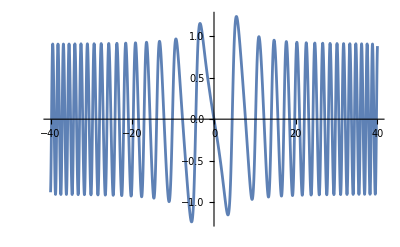

## Resolución del sistema por pasos

Ecuación diferencial para α_+

```mathematica
alphaMas= NDSolveValue[{y'[t]- I Ω  y[t]^2 + 2 I  (β^2)t y[t] + I  Ω==0,y[0]==0}, y, {t,-40,40}]
```

InterpolatingFunction[…]

```mathematica
Plot[Im[alphaMas[t]], {t, -40, 40}]
```

-Graphics-

```mathematica
alphaMas[12]
```

0.57469+0.25698 ⅈ

Ecuación diferencial para α_z

```mathematica
alphaZ[T_] := I(Ω NIntegrate[alphaMas[t], {t, 0 , T}] - (β^ 2)( T^2)( 0.5))
```

```mathematica
alphaZ[30]
```

0.335219-30.2466 ⅈ

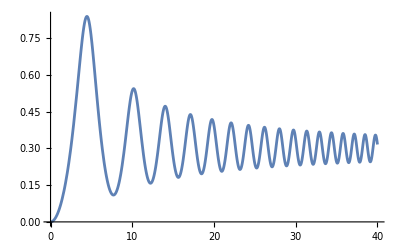

```mathematica
Plot[Re[alphaZ[t]], {t, 0, 40}]
```

A partir de la expresión para α_z creamos una tabla de valores y los interpolamos para obtener una “función numerica integrable” de α_z

```mathematica
alphaZInter = Interpolation[Table[alphaZ[t],{t,0,30}]]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[alphaZInter[t], {t, 1, 10}]
```

3.02247-13.2524 ⅈ

Ecuación diferencial para α_-

```mathematica
alphaMenos[T_] := -I Ω NIntegrate[Exp[2 alphaZInter[t]], {t, 1, T}]
```

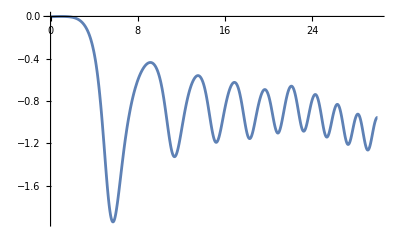

```mathematica
Plot[Re[alphaMenos[t]], {t, 0, 30}]
```

## Resolución del sistema completo

```mathematica
Clear[alphaMas, alphaMenos, alphaZ]
```

En la siguiente celda ejecutamos el comando NDSolveValue para resolver el sistema completo de ecuaciones diferenciales de forma númerica. En esta expresión las funciones x(t), y(t), z(t) representan las funciones α_+(t), α_z(t) y α_-(t) respectivamente.

```mathematica
{alphaMas,alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + I Ω(1 + x[t]^2)== 0 ,y'[t] == I(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ I Ω == 0, x[-40]==y[-40]==z[-40]== 0},{x,y, z},{t,-60, 60}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

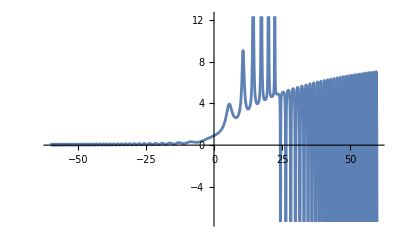

```mathematica
Plot[Re[alphaMas[t]], {t, -60, 60}]
```

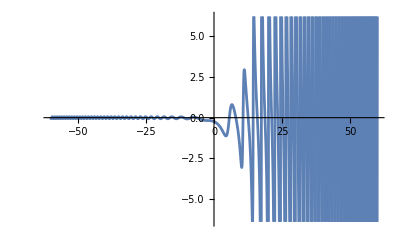

```mathematica
Plot[Im[alphaMas[t]], {t, -60, 60}]
```

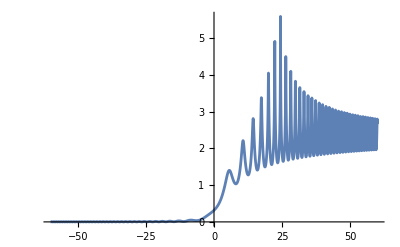

```mathematica
Plot[Re[alphaZ[t]], {t, -60, 60}]
```

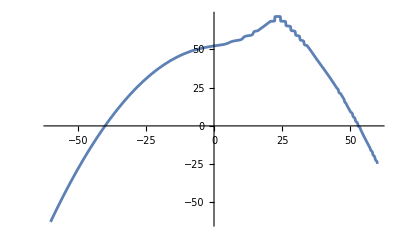

```mathematica
Plot[Im[alphaZ[t]], {t, -60, 60}]
```

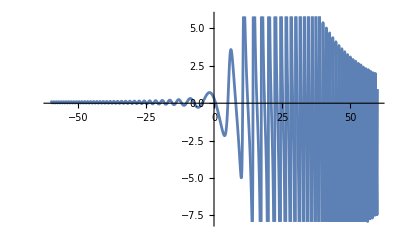

```mathematica
Plot[Re[alphaMenos[t]], {t, -60, 60}]
```

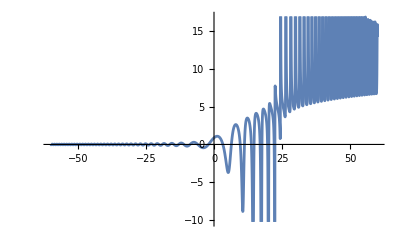

```mathematica
Plot[Im[alphaMenos[t]], {t, -60, 60}]
```

### Probabilidades de Transición

Probabilidad de ir del estado base al estado excitado considerando que el estado inicial es el estado base (P_g->e(t))

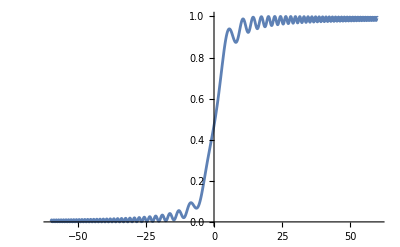

```mathematica
Plot[(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], {t, -60, 60}]
```

Probabilidad de transición al estado base considerando que el estado inicial es el estado base (P_g->g(t))

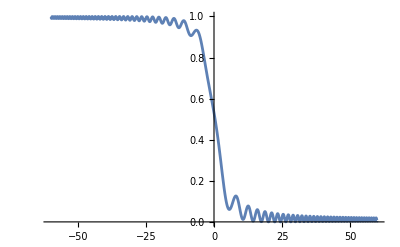

```mathematica
Plot[Abs[Exp[- alphaZ[t]] ]^2, {t, -60, 60}]
```

Ambas funciones en un mismo grafico

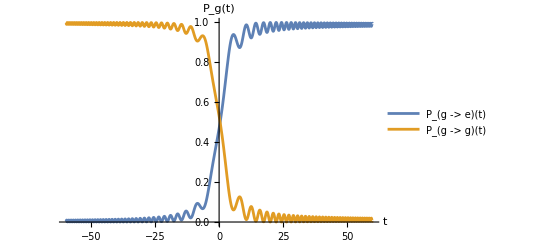

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2,}, {t, -60, 60}, 
PlotLegends-> {"P_(g -> e)(t)", "P_(g -> g)(t)"}, 
AxesLabel-> {"t", "P_g(t)"}]
```

Probabilidad de ir del estado excitado al estado base considerando que el estado inicial es el estado excitado (P_e->g(t))

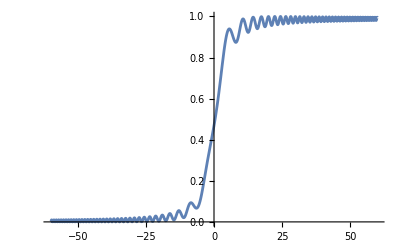

```mathematica
Plot[(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], {t, -60, 60}]
```

Probabilidad de transición al estado excitado considerando que el estado inicial es el estado excitado (P_e->e(t))

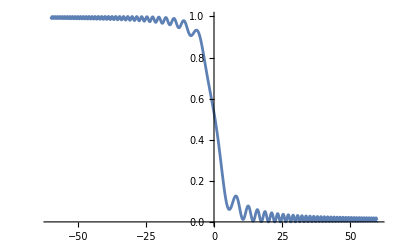

```mathematica
Plot[Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2, {t, -60, 60}]
```

Ambas funciones en un gráfico

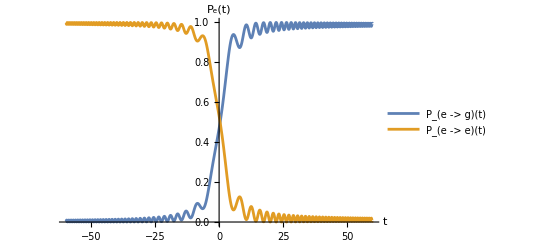

```mathematica
Plot[{(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2}, {t, -60, 60}, 
PlotLegends-> {"P_(e -> g)(t)", "P_(e -> e)(t)"}, AxesLabel-> {"t", "P_e(t)"}]
```